# Impact of Corpus Size on Quality of Frequency Table

## Jeffrey Starr - 2013 October 12

## Hypothesis

The reverse Huffman steganography technique uses as input a n-character long frequency table drawn from a corpus. We know that the quality of the output increases as n grows, albeit not monotonically. n cannot grow beyond the size of the corpus and the number of branches declines as n grows leading to greater spatial inefficiency in the encoding process. We hypothesize that there are similar declines in the marginal improvement as the corpus size, s, increases.

## Approach

During the encoding process, the algorithm walks through a Huffman encoding of the frequency list to determine what tokens to emit based on a binary interpretation of the input. The actual frequency values are relatively unimportant; it is the frequency values in relation to each other that impact how the Huffman tree is generated. To measure quality, we will compare the frequency tables for different sizes of s, where the different versions of the corpus are drawn from the same work.

As our distance measure, we will use the Euclidean distance of the normalized frequency vectors. The tokens represent dimensions and the frequency counts are the lengths. For instance, the distance between u={a:4, b:2, c:1} and v={a:8, b:4, c:2} is zero.

```mathematica
FreqTableDistance[u_List,v_List]:=
With[{ud=StandardizeDimensions[u,v],
vd=StandardizeDimensions[v,u]},
EuclideanDistance[
Normalize[ud],
Normalize[vd]
]
]
```

StandardizeDimensions takes two frequency lists, u and v, and returns the frequency counts of u, in sorted order by the union of tokens from u and v.

```mathematica
StandardizeDimensions[u_List,v_List]:=
If[OrderedQ[u]∧OrderedQ[v],
With[{dimensions=Union[#[[1]]&/@u,#[[1]]&/@v]},
StandardizeDimensionsHelper[u,dimensions,{}]],
Print["u and v must be in sorted order"]
]
```

Iterate through dimensions and, if u has a matching token, emit the frequency count in the table, else emit zero.

```mathematica
StandardizeDimensionsHelper[u_List,dimensions_List,fcounts_List]:=
Switch[u,
{},
Switch[dimensions,
{},
fcounts,
_,
StandardizeDimensionsHelper[{},Rest[dimensions],Append[fcounts,0]
]
],
{__},
Switch[First[u][[1]],
First[dimensions],
StandardizeDimensionsHelper[Rest[u],Rest[dimensions],Append[fcounts,First[u][[2]]]
],
_,
StandardizeDimensionsHelper[u,Rest[dimensions],Append[fcounts,0]]
]
]
```

Verify that we get the frequency counts from u (simple input where dimensions match between the two cases):

```mathematica
StandardizeDimensions[{{"ab",4},{"bc",3}},{{"ab",5},{"bc",6}}]
```

{4,3}

Verify u can have more tokens than v.

```mathematica
StandardizeDimensions[{{"ab",4},{"bc",3},{"cd",1}},{{"ab",5},{"bc",6}}]
```

{4,3,1}

Verify u can have fewer tokens than v.

```mathematica
StandardizeDimensions[{{"ab",4}},{{"ab",5},{"bc",6}}]
```

{4,0}

Verify u can be empty.

```mathematica
StandardizeDimensions[{},{{"ab",5},{"bc",6}}]
```

{0,0}

## Corpus

Mathematica comes with a variety of built-in corpora. We will use Darwin’s Origin of Species since it is one of the largest works at 893,000 characters in length. In order to obtain a set of corpora with non-overlapping and growing size, we will partition the text into 88 chunks of 10,149 characters. Then, we will combine the chunks via the Fibonacci sequence (such that the first corpora is equal to the first chunk, the second corpora is equal to the second chunk, the third corpora is equal to the third and fourth chunks concatenated together, and so on. The ninth corpora is equal to the last 34 chunks).

```mathematica
StringLength[ExampleData[{"Text","OriginOfSpecies"},"String"]]
```

893121

```mathematica
FactorInteger[893000]
```

{{2,3},{5,3},{19,1},{47,1}}

```mathematica
fibos=Table[Fibonacci[i],{i,10}]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
Accumulate[fibos]
```

{1,2,4,7,12,20,33,54,88,143}

```mathematica
893121/88//N
```

10149.1

```mathematica
chunks=Partition[
Characters[
ExampleData[{"Text","OriginOfSpecies"},"String"]
],Floor[893121/88]
];
```

```mathematica
Length[chunks]
```

88

```mathematica
PartitionByFibonacci[parts_,{},i_Integer]:=
parts
```

```mathematica
PartitionByFibonacci[parts_List,chunks_,i_Integer]:=
PartitionByFibonacci[
Append[parts,StringJoin[Flatten[Take[chunks,Fibonacci[i]]]]],
Drop[chunks,Fibonacci[i]],
i+1]
```

```mathematica
corpora=PartitionByFibonacci[{},chunks,1];
```

```mathematica
Length[corpora]
```

9

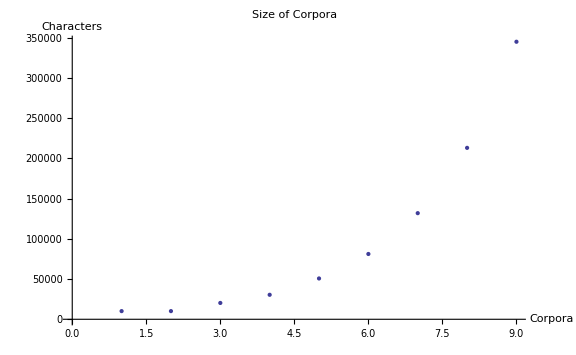

```mathematica
ListPlot[StringLength/@corpora,
PlotLabel->"Size of Corpora",
AxesLabel->{"Corpora","Characters"},
ImageSize->Large]
```

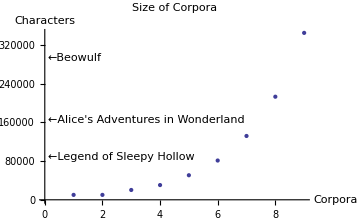

```mathematica
Show[
ListPlot[StringLength/@corpora,
PlotLabel->"Size of Corpora",
AxesLabel->{"Corpora","Characters"},
ImageSize->Medium],
Graphics[{
Text["←Legend of Sleepy Hollow",{0.1,89000},{-1,0}],
Text["←Alice's Adventures in Wonderland",{0.1,164000},{-1,0}],
Text["←Beowulf",{0.1,294000},{-1,0}]
}]
]
```

```mathematica
Total[StringLength/@corpora]
```

893112

### Corpora Frequency Tables

```mathematica
CorporaFreqTable[n_]:=
Table[
Sort[
Tally[
Partition[Characters[c],n,1]
]/.{tokens_List,count_Integer}:>{StringJoin[tokens],count}
],
{c,corpora}
]
```

Corporaft is a list of frquency tables for n=2 to 5 (inclusive).

```mathematica
corporaft=
Table[
CorporaFreqTable[n],
{n,2,5}];
```

GetFrequencyTable returns the frequency table for a given n and a segment (1 through 9).

```mathematica
GetFrequencyTable[n_,cs_]:=
corporaft[[n-1]][[cs]]
```

## Distance between Corpora Sets

```mathematica
TriangularDistanceTable[n_]:=
TableForm[
ParallelTable[
If[i<j,
N[FreqTableDistance[GetFrequencyTable[n,i],GetFrequencyTable[n,j]],3],
" "
],
{i,1,9},{j,2,9}
],
TableHeadings->{Range[1,8],Range[2,9]}
]
```

```mathematica
TriangularDistanceTable[2]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 0.206 | 0.206 | 0.194 | 0.202 | 0.166 | 0.174 | 0.162 | 0.172
2 |   | 0.219 | 0.205 | 0.213 | 0.19 | 0.188 | 0.184 | 0.189
3 |   |   | 0.128 | 0.152 | 0.165 | 0.132 | 0.131 | 0.138
4 |   |   |   | 0.149 | 0.144 | 0.122 | 0.114 | 0.138
5 |   |   |   |   | 0.15 | 0.105 | 0.132 | 0.127
6 |   |   |   |   |   | 0.107 | 0.0956 | 0.104
7 |   |   |   |   |   |   | 0.089 | 0.0857
8 |   |   |   |   |   |   |   | 0.0838
 |   |   |   |   |   |   |   |

```mathematica
Block[{$IterationLimit=Infinity},TriangularDistanceTable[3]]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 0.387 | 0.381 | 0.377 | 0.351 | 0.306 | 0.301 | 0.303 | 0.304
2 |   | 0.383 | 0.371 | 0.387 | 0.332 | 0.334 | 0.328 | 0.346
3 |   |   | 0.243 | 0.307 | 0.303 | 0.262 | 0.265 | 0.272
4 |   |   |   | 0.312 | 0.277 | 0.256 | 0.243 | 0.265
5 |   |   |   |   | 0.276 | 0.216 | 0.258 | 0.254
6 |   |   |   |   |   | 0.196 | 0.191 | 0.203
7 |   |   |   |   |   |   | 0.176 | 0.159
8 |   |   |   |   |   |   |   | 0.155
 |   |   |   |   |   |   |   |

```mathematica
Block[{$IterationLimit=Infinity},TriangularDistanceTable[4]]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 0.555 | 0.545 | 0.535 | 0.495 | 0.44 | 0.436 | 0.439 | 0.429
2 |   | 0.539 | 0.522 | 0.547 | 0.472 | 0.478 | 0.469 | 0.487
3 |   |   | 0.367 | 0.455 | 0.433 | 0.383 | 0.388 | 0.394
4 |   |   |   | 0.454 | 0.399 | 0.373 | 0.359 | 0.382
5 |   |   |   |   | 0.392 | 0.317 | 0.369 | 0.362
6 |   |   |   |   |   | 0.282 | 0.272 | 0.28
7 |   |   |   |   |   |   | 0.256 | 0.225
8 |   |   |   |   |   |   |   | 0.227
 |   |   |   |   |   |   |   |

```mathematica
ParallelEvaluate[$IterationLimit=Infinity]
```

{∞,∞,∞,∞}

```mathematica
TriangularDistanceTable[5]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 0.756 | 0.728 | 0.72 | 0.66 | 0.61 | 0.599 | 0.603 | 0.581
2 |   | 0.704 | 0.684 | 0.71 | 0.624 | 0.63 | 0.616 | 0.636
3 |   |   | 0.517 | 0.608 | 0.584 | 0.52 | 0.53 | 0.532
4 |   |   |   | 0.607 | 0.545 | 0.506 | 0.495 | 0.519
5 |   |   |   |   | 0.515 | 0.423 | 0.484 | 0.472
6 |   |   |   |   |   | 0.379 | 0.374 | 0.381
7 |   |   |   |   |   |   | 0.342 | 0.298
8 |   |   |   |   |   |   |   | 0.312
 |   |   |   |   |   |   |   |

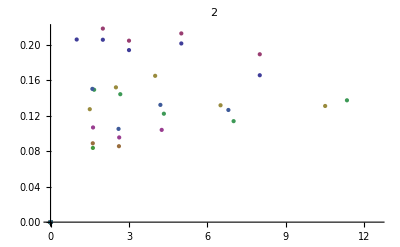
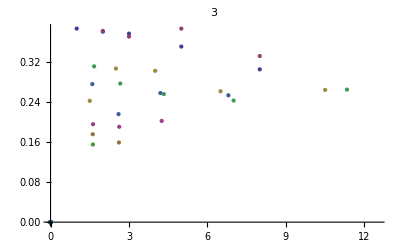
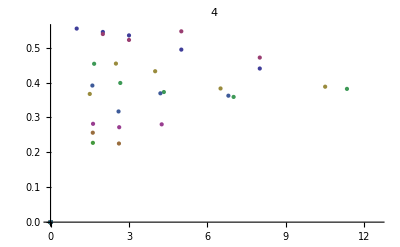
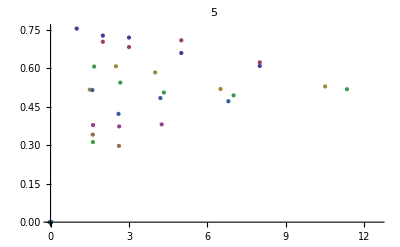

```mathematica
Table[
ListPlot[
ParallelTable[
If[i<j,
{StringLength[corpora[[j]]]/StringLength[corpora[[i]]],
FreqTableDistance[GetFrequencyTable[n,i],GetFrequencyTable[n,j]]},
{0,0}
],
{i,1,9},{j,1,9}
],
PlotLabel->n
],
{n,2,5}
]
```

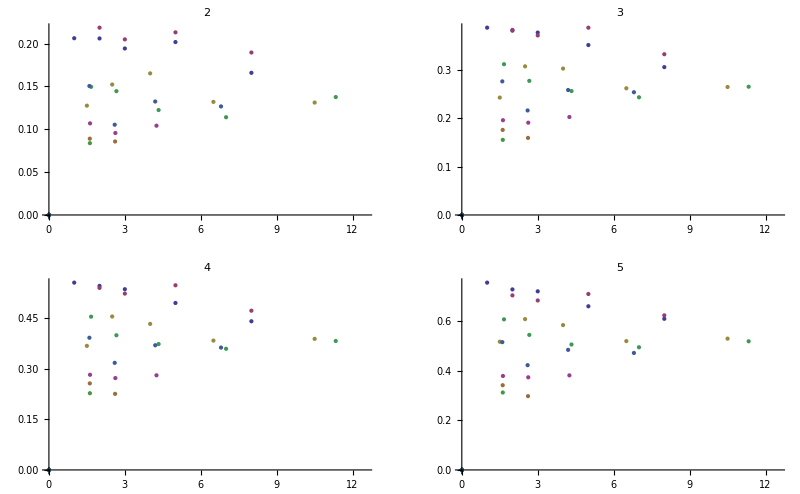

```mathematica
GraphicsGrid[Partition[%26,2]]
```

```mathematica
ListPlot3D[
ParallelTable[
If[i<j,
FreqTableDistance[GetFrequencyTable[3,i],GetFrequencyTable[3,j]],
0
],
{i,1,9},{j,1,9}
]
]
```

-Graphics3D-